```mathematica
plotstuff[a_]:=
(Graphics[{Circle[#[[1]],0.5],Text[#[[2]],#[[1]]]}&/@({Partition[a,2],Table[ToString[k],{k,1,7}]}//Transpose)]);
plotstuffsized[a_,size_]:=Image[plotstuff[a],ImageSize->{size,size}]
```

```mathematica
postable=Import["/home/abe/uu/comsys/pos.txt","table"];
energytable=Import["/home/abe/uu/comsys/energy.txt","table"];
```

```mathematica
Table[plotstuff[postable[[k]]],{k,9,900,9*5}];
```

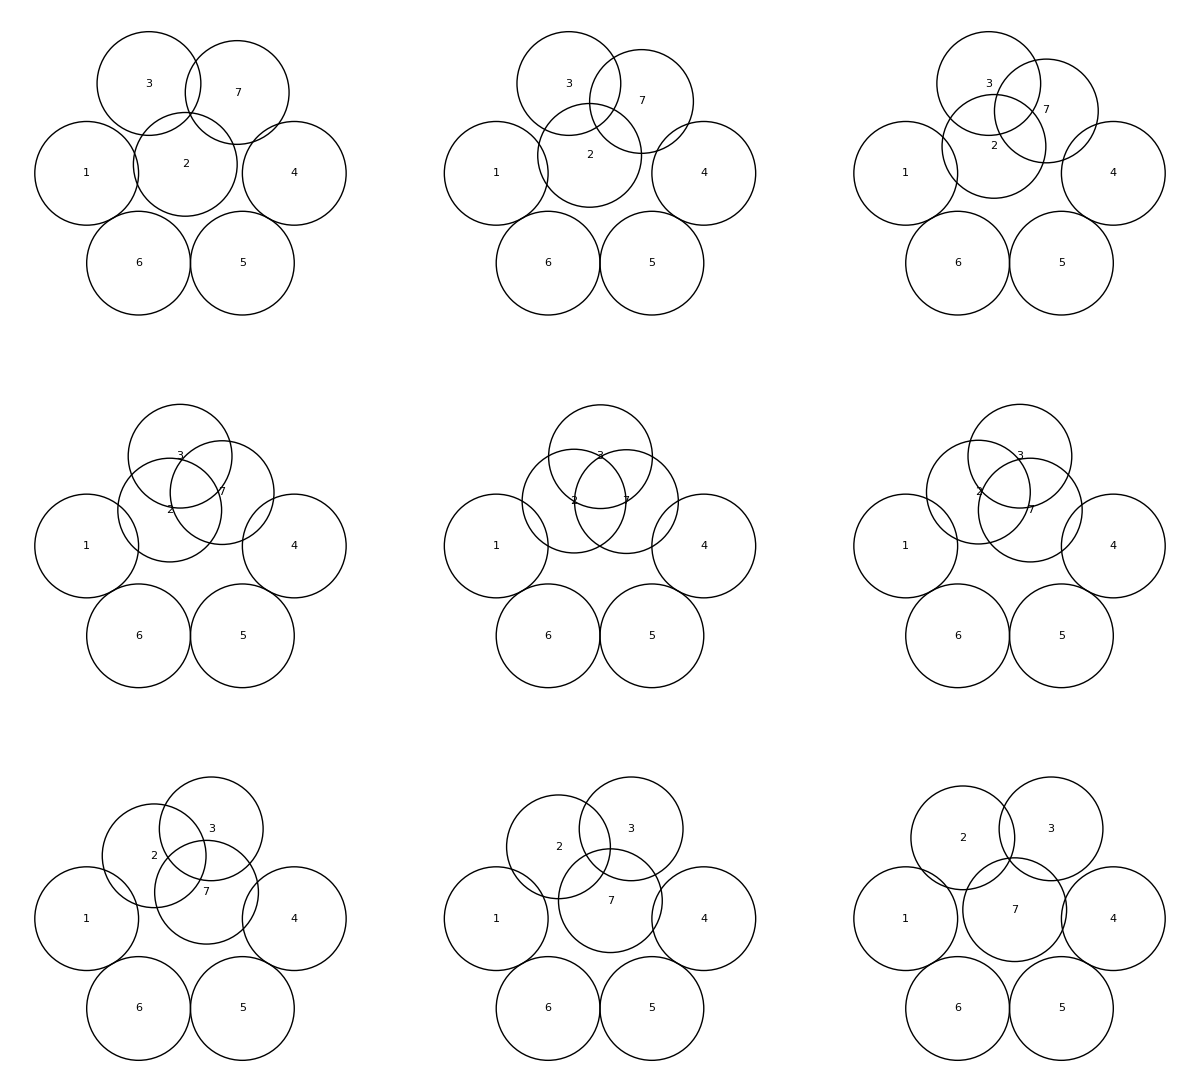

```mathematica
Partition[Table[plotstuff[postable[[k]]],{k,1,9,1}],3]//GraphicsGrid
```

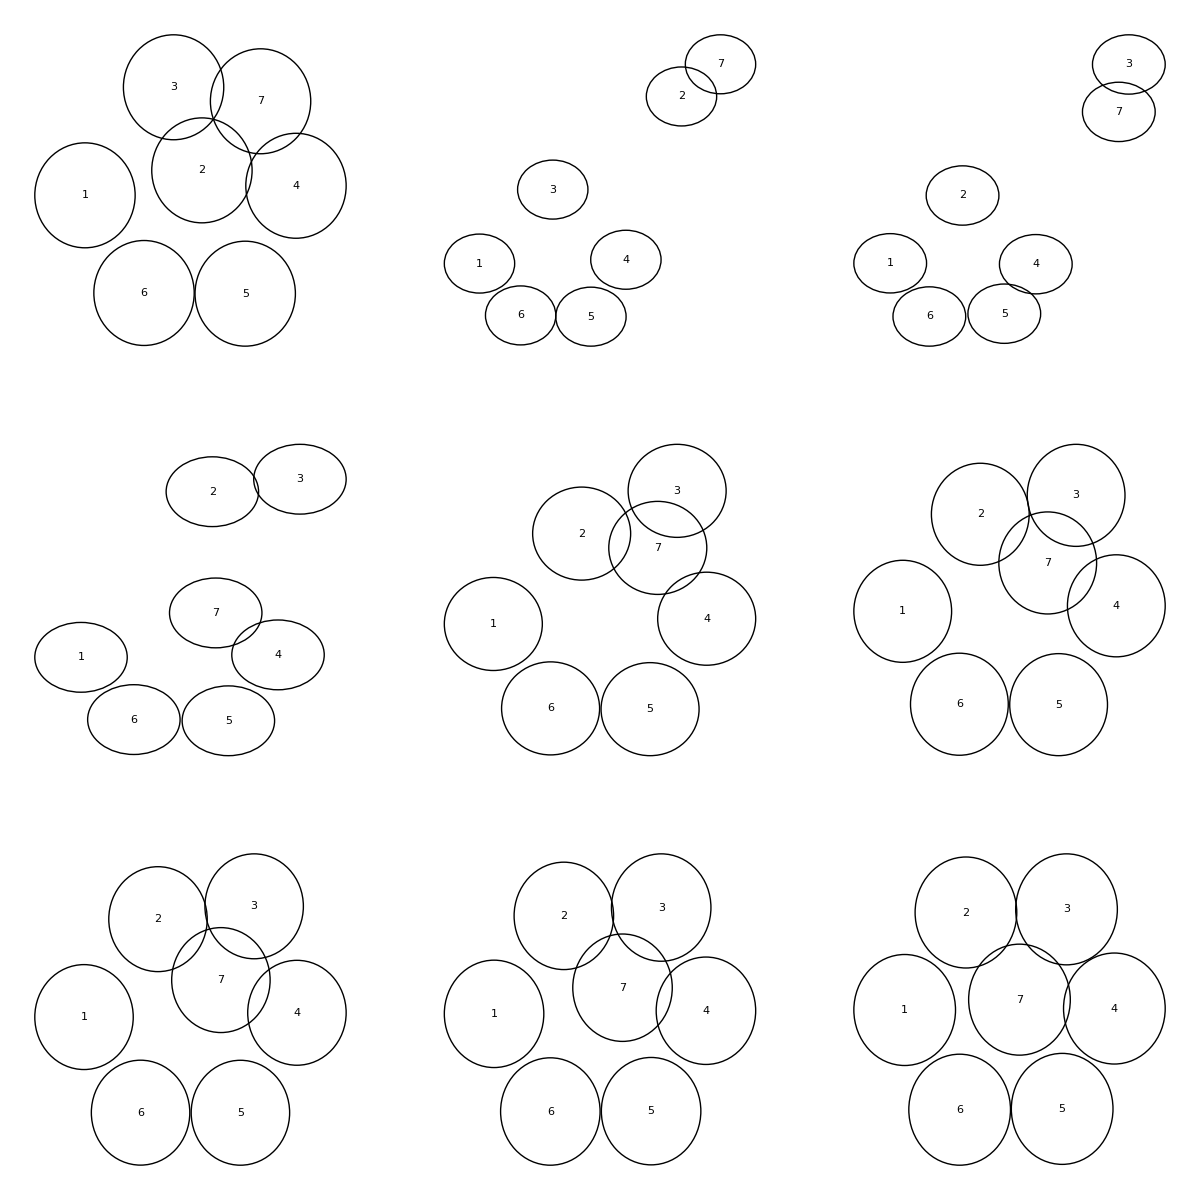

```mathematica
Partition[Table[plotstuff[postable[[k]]],{k,-18,-10,1}],3]//GraphicsGrid
```

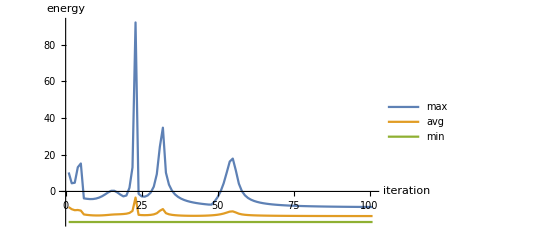

```mathematica
energyplot=ListPlot[{Max/@energytable,Mean/@energytable,Min/@energytable},PlotRange->Full,Joined->True,AxesLabel->{"iteration","energy"},PlotLegends->{"max","avg","min"}]
```

```mathematica
animation=Table[ImageAssemble[Partition[Table[plotstuffsized[postable[[k]],60],{k,1+iter*9,9+iter*9,1}],3]],{iter,0,99,1}];
```

```mathematica
Animate[animation[[k]],{k,1,Length[animation],1}]
```

```mathematica
Export["moving_particles.gif",animation,ImageSize->{60*3,60*3}]
```

moving_particles.gif

```mathematica
Export["energy_vs_iteration.png",energyplot]
```

energy_vs_iteration.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["moving_particles.gif"]]]
```